```mathematica
foldname="C:\\Users\\msztr\\OneDrive\\Documents\\GitHub\\VeriGudGame\\Measurements\\Aluminium_Big"
filenms = FileNames[All,foldname];
```

C:\Users\msztr\OneDrive\Documents\GitHub\VeriGudGame\Measurements\Aluminium_Big

```mathematica
samplerate=125 10^6;
```

```mathematica
res=Table[dat=Import[filenms[[i]]][[5;;-1]];
dat1={#[[1]]/samplerate,#[[2]]}&/@dat[[All,1;;2]];
dat2={#[[1]]/samplerate,#[[2]]}&/@dat[[All,{1,3}]];
fit1 = NonlinearModelFit[dat1, a Sin[b t+ c] + d  , {{a,Max[dat1[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat1,Last][[1,1]]/Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
fit2 = NonlinearModelFit[dat2, a Sin[b t+ c] + d , {{a,Max[dat2[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat2,Last][[1,1]]/Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
Flatten[{Transpose[{fit1["BestFitParameters"][[All,2]],fit1["ParameterErrors"]}],Transpose[{fit2["BestFitParameters"][[All,2]],fit2["ParameterErrors"]}]}],{i,1,Length[filenms]}]
Export[foldname<>"_results.xlsx",res]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{{0.0562626,0.000239794,3.92686×10^6,1193.6,25.2372,0.00847797,0.000273451,0.000168978,2.50544,0.00217271,3.92699×10^6,253.534,1.19855,0.00177717,-0.062597,0.00154756},{-0.0517304,0.000207539,1.57114×10^6,1224.54,1.37414,0.00851917,0.000333278,0.000152282,-2.49709,0.000975543,1.57077×10^6,107.661,6.14207,0.000758911,-0.0630416,0.000682955},{0.0540095,0.000208894,1.60984×10^6,1222.47,10.5629,0.00846727,0.000287294,0.000154292,-2.49794,0.00103668,1.6101×10^6,110.13,5.90426,0.000780511,-0.0641066,0.000720057},{0.0562318,0.000205536,1.64974×10^6,1171.06,16.5974,0.00809203,0.00035768,0.000151709,-2.49801,0.00108531,1.64932×10^6,112.974,5.66523,0.000803219,-0.0642496,0.0007514},{0.0588259,0.000194324,1.68846×10^6,1046.62,3.7901,0.00723073,0.000419667,0.000142311,2.4967,0.00112253,1.68865×10^6,116.878,8.5646,0.000831411,-0.0626164,0.000778178},{-0.0126346,0.00161021,2.44544×10^6,34174.4,5.46489,0.241567,-0.00427719,0.00112677,2.49763,0.0011258,1.72784×10^6,119.418,8.32806,0.000847557,-0.063191,0.000784625},{0.064283,0.000200229,1.76722×10^6,916.017,3.29857,0.00636506,0.000444725,0.000142864,2.49683,0.00113765,1.76723×10^6,124.925,8.08553,0.000882947,-0.0637674,0.000799748},{-0.0672529,0.00021251,1.80581×10^6,890.121,6.19851,0.00621521,0.000197785,0.000149959,2.49765,0.00113457,1.8065×10^6,129.931,1.56425,0.000913359,-0.0646189,0.000805997},{-0.0704052,0.000217751,1.84549×10^6,840.075,12.2351,0.00589767,0.0003472,0.000152511,2.49772,0.00113342,1.84572×10^6,135.271,1.32561,0.000945962,-0.0643711,0.000813531},{0.0737209,0.000220046,1.88493×10^6,793.192,21.409,0.00559355,0.000399855,0.000153668,2.49816,0.00112724,1.88491×10^6,138.715,1.0835,0.000966355,-0.0638834,0.000815242},{0.0774979,0.000224606,1.92447×10^6,766.572,21.1645,0.00542331,0.000268962,0.000157063,2.49808,0.00113817,1.92431×10^6,141.877,0.844996,0.000986399,-0.0638358,0.000825226},{0.0813244,0.000223515,1.96349×10^6,736.258,20.9171,0.00521486,0.000379017,0.000157094,2.49892,0.00114048,1.96351×10^6,140.99,0.605088,0.000980571,-0.0648047,0.000824138},{0.0857752,0.000221244,2.00267×10^6,709.751,14.3862,0.00502283,0.000328971,0.000156726,2.49668,0.00117926,2.00266×10^6,142.232,0.367644,0.000991729,-0.0649765,0.000845434},{0.090168,0.000224933,2.0423×10^6,711.313,7.85529,0.0050195,0.000371377,0.000160844,2.49793,0.00118818,2.04206×10^6,138.153,0.130125,0.000967376,-0.0639525,0.000843351},{0.095216,0.000217795,2.08171×10^6,676.209,1.31871,0.00475369,0.000402243,0.000157126,-2.49835,0.00121699,2.08126×10^6,136.273,3.02977,0.000958524,-0.0618056,0.00085574},{-0.100452,0.000216004,2.12065×10^6,653.647,23.0548,0.00457542,0.000348491,0.00015677,-2.49755,0.00123903,2.12053×10^6,134.534,2.7865,0.000950216,-0.0624042,0.000865179},{-0.106443,0.000217028,2.15997×10^6,628.624,16.5222,0.00437909,0.000288992,0.000157776,-2.49721,0.00126441,2.15982×10^6,134.732,2.55081,0.000954612,-0.0636577,0.000879692},{-0.113038,0.000228469,2.19896×10^6,621.083,16.2663,0.00430964,0.00034504,0.000165534,-2.49625,0.00125461,2.19908×10^6,133.253,2.30919,0.000945124,-0.0642607,0.000872857},{0.120296,0.000231605,2.23835×10^6,580.824,31.7178,0.00401977,0.000275205,0.000166615,-2.49594,0.00130356,2.2384×10^6,140.111,2.07178,0.000992655,-0.0627366,0.000909991},{0.128217,0.000227086,2.27776×10^6,519.454,0.0425651,0.00359302,0.000342405,0.000161943,2.49617,0.00127676,2.27765×10^6,140.625,4.97461,0.000993398,-0.0639612,0.000896836},{-0.137314,0.000230635,2.31694×10^6,477.845,9.20467,0.00331078,0.00029692,0.000163158,2.49505,0.00128514,2.31694×10^6,146.245,4.73308,0.00102909,-0.0634007,0.000909974},{-0.147212,0.000233138,2.35604×10^6,439.091,2.65583,0.00305425,0.000316136,0.000163984,2.49345,0.00129209,2.35619×10^6,152.043,4.49344,0.00106545,-0.0641406,0.000922436},{-0.158694,0.000234817,2.39549×10^6,403.581,2.38863,0.00282401,0.00041183,0.000164707,2.49274,0.00129567,2.39544×10^6,156.539,4.25859,0.001093,-0.066416,0.000931003},{-0.171608,0.000243629,2.43474×10^6,385.953,2.10994,0.00271871,0.000221784,0.000170989,2.49076,0.00129802,2.43466×10^6,159.012,4.01537,0.00110812,-0.0632047,0.000935424},{0.186355,0.000250611,2.47407×10^6,368.855,4.96878,0.00261575,0.000314283,0.000176474,2.48772,0.00131782,2.47401×10^6,161.172,3.77527,0.00112287,-0.0645239,0.00094829},{0.203088,0.000253953,2.51325×10^6,349.063,10.9618,0.00248907,0.000302448,0.000179727,-2.48451,0.00136028,2.51333×10^6,163.677,6.67654,0.00114205,-0.0639162,0.000973621},{0.222233,0.000259083,2.55234×10^6,331.913,4.37842,0.0023746,0.000131715,0.000184277,-2.48043,0.00141628,2.55253×10^6,166.107,6.43688,0.0011624,-0.0643139,0.00100612},{-0.243888,0.00026605,2.59182×10^6,314.956,13.4926,0.00225352,0.000191189,0.0001898,-2.47541,0.00148468,2.59185×10^6,169.277,6.20055,0.00118918,-0.0648833,0.00104663},{0.267875,0.000276279,2.63098×10^6,298.192,3.73543,0.00212673,0.000169839,0.000196949,-2.46808,0.00153303,2.63109×10^6,170.722,-0.325284,0.00120354,-0.0642077,0.00107405},{0.293614,0.000290408,2.67028×10^6,282.605,28.5181,0.00200263,0.000159745,0.000206152,-2.46155,0.00158435,2.67029×10^6,173.827,5.71791,0.00122885,-0.0620211,0.00110593},{-0.306662,0.000305302,2.68987×10^6,281.855,6.34301,0.00198952,0.000167421,0.000216115,2.45552,0.00158852,2.68998×10^6,173.953,8.73788,0.00123082,-0.0621538,0.00110802},{-0.319608,0.0002976,2.70966×10^6,261.272,6.15698,0.00183672,0.000292066,0.000210116,2.452,0.00157965,2.70966×10^6,173.032,8.62143,0.0012249,-0.0642387,0.00110184},{0.331677,0.000310221,2.72924×10^6,260.35,21.6718,0.00182363,0.0000541846,0.000218536,2.44708,0.00160545,2.72928×10^6,176.583,8.50303,0.00125004,-0.0631951,0.00112066},{0.342165,0.000316552,2.74892×10^6,256.175,21.4729,0.00178927,0.000086501,0.000222673,2.44262,0.00161415,2.74893×10^6,178.794,8.38237,0.00126518,-0.0645886,0.00112836},{-0.344913,0.000319858,2.75677×10^6,256.41,5.67847,0.00178967,0.000223696,0.000224905,2.43968,0.0016166,2.75681×10^6,179.802,8.33433,0.00127194,-0.0634457,0.00113093},{0.348245,0.000323574,2.76459×10^6,256.852,8.74027,0.00179157,0.0000647991,0.000227498,2.43847,0.00162268,2.76467×10^6,181.167,8.28817,0.00128109,-0.0650134,0.00113615},{0.351421,0.000324599,2.77248×10^6,255.415,8.65594,0.0017809,0.000128797,0.000228227,-2.43611,0.00160402,2.77244×10^6,179.917,23.9478,0.00127178,-0.063763,0.00112413},{-0.354232,0.000328981,2.78025×10^6,257.1,30.5647,0.00179234,0.000111425,0.000231366,2.43412,0.0016051,2.78036×10^6,180.925,8.19312,0.00127825,-0.06286,0.00112605},{0.356448,0.000333973,2.78811×10^6,259.85,8.4875,0.00181171,0.000211078,0.000234975,2.43462,0.00161108,2.78817×10^6,182.361,8.14387,0.00128782,-0.0642506,0.00113149},{0.358288,0.000328585,2.79603×10^6,255.011,14.6836,0.00177855,0.000172394,0.000231326,2.43347,0.00162564,2.79596×10^6,184.956,8.09465,0.00130552,-0.0658806,0.00114305},{-0.359713,0.000327116,2.80382×10^6,253.717,30.3087,0.00177023,-0.00003753,0.000230477,2.43334,0.00162138,2.80378×10^6,185.389,8.0491,0.00130771,-0.0631169,0.00114145},{0.360705,0.000336203,2.81167×10^6,261.063,8.2275,0.00182297,0.0000650194,0.0002371,2.43124,0.00161371,2.8117×10^6,185.635,1.71368,0.00130884,-0.0636236,0.00113752},{0.361046,0.000332268,2.81967×10^6,258.964,8.14217,0.00180959,-0.0000637199,0.000234589,2.43048,0.00160807,2.81961×10^6,186.038,1.666,0.0013108,-0.0635771,0.00113506},{0.360966,0.000327259,2.82734×10^6,256.362,39.4759,0.00179281,0.000262855,0.000231328,2.43005,0.00160792,2.82742×10^6,187.062,1.62158,0.00131695,-0.0644694,0.00113648},{0.086271,0.00894172,3.58235×10^6,30042.,12.8348,0.211061,-0.00171389,0.00634857,2.42892,0.00161564,2.83536×10^6,189.097,1.5728,0.00133038,-0.0637482,0.00114352},{0.359146,0.000327603,2.84318×10^6,260.743,14.1711,0.00182689,-0.0000869347,0.00023219,2.4294,0.00160313,2.84313×10^6,188.623,1.52498,0.00132615,-0.0622084,0.00113621},{0.357359,0.000329447,2.85099×10^6,264.969,7.79969,0.00185851,-9.22104×10^-7,0.000233814,2.43081,0.00162673,2.85098×10^6,192.341,1.47641,0.0013514,-0.0640505,0.00115452},{-0.355462,0.000327672,2.85889×10^6,266.393,17.1429,0.00186985,0.000181267,0.000232871,2.43054,0.00162598,2.8588×10^6,193.312,1.43121,0.00135714,-0.0643001,0.00115554},{0.352832,0.00032484,2.86668×10^6,267.428,1.35053,0.00187864,0.0000664368,0.000231157,2.43073,0.00162081,2.86675×10^6,193.716,1.38245,0.00135905,-0.0636875,0.00115341},{0.350012,0.000321544,2.87458×10^6,268.138,1.26548,0.00188494,0.0000960509,0.000229092,2.43196,0.00163536,2.8745×10^6,196.341,1.33381,0.00137664,-0.0631682,0.00116523},{0.346524,0.000322443,2.88242×10^6,272.758,1.18053,0.00191853,0.00013503,0.000229983,2.43198,0.00161956,2.88242×10^6,195.397,1.28457,0.00136917,-0.0621321,0.00115539},{0.342811,0.000317915,2.89028×10^6,272.848,32.5127,0.00191989,0.0000590318,0.000226969,2.43451,0.00161481,2.89035×10^6,195.525,32.6511,0.00136925,-0.0605122,0.00115333},{0.338728,0.000317595,2.89817×10^6,276.708,1.01455,0.00194733,0.000146491,0.00022692,-2.43497,0.00162385,2.89811×10^6,197.414,23.1783,0.0013817,-0.0629658,0.00116101},{0.334563,0.000317605,2.90598×10^6,280.852,0.936895,0.00197622,0.0000447036,0.000227071,2.43627,0.00162221,2.906×10^6,197.887,1.14205,0.00138411,-0.0629667,0.00116097},{0.330046,0.000311518,2.91376×10^6,279.656,0.853711,0.00196752,0.0000685327,0.000222808,2.43832,0.00161785,2.91381×10^6,197.876,1.09099,0.00138345,-0.0639352,0.00115883},{0.325308,0.000311901,2.92162×10^6,284.403,32.1938,0.00199983,0.0000699593,0.000223149,2.43992,0.00161761,2.92162×10^6,198.327,1.04735,0.00138583,-0.0623402,0.00115952},{0.320329,0.000304628,2.92953×10^6,282.161,0.698401,0.00198281,0.000155419,0.000217964,2.44062,0.00163214,2.92947×10^6,200.573,0.998717,0.00140097,-0.0628513,0.00117066},{-0.315329,0.000302704,2.93735×10^6,284.722,16.3291,0.00199917,0.000281266,0.000216572,2.444,0.00161944,2.93735×10^6,199.162,0.949819,0.00139061,-0.062596,0.00116212},{0.310277,0.000306594,2.94531×10^6,292.843,25.6781,0.00205408,0.000151184,0.000219316,2.44516,0.0016301,2.94522×10^6,200.704,0.902776,0.00140094,-0.0632074,0.00117018},{0.304937,0.000302748,2.9531×10^6,293.738,0.46692,0.00205814,0.000178734,0.00021648,2.44718,0.00163404,2.95302×10^6,201.237,0.85169,0.00140434,-0.0638941,0.00117324},{0.0678171,0.00763553,3.69039×10^6,31312.2,-0.857341,0.2191,0.0059062,0.00537016,2.44842,0.00163582,2.96093×10^6,201.47,0.804397,0.00140568,-0.0629632,0.00117458},{0.294698,0.00030582,2.96897×10^6,305.949,0.323137,0.00213793,0.00010498,0.000218496,2.45039,0.0016575,2.9688×10^6,203.985,0.758382,0.00142304,-0.0619782,0.00119006},{0.0645309,0.00735701,3.70653×10^6,31720.3,-1.01467,0.222283,0.00584704,0.00517587,2.45336,0.00163958,2.97664×10^6,201.436,0.712537,0.00140518,-0.0625118,0.00117692},{-0.284166,0.000298,2.98451×10^6,307.673,9.60545,0.00214383,0.000245517,0.000212669,2.45465,0.00164025,2.98446×10^6,201.206,0.664305,0.00140357,-0.0637494,0.00117696},{0.271005,0.000295571,3.00411×10^6,317.847,18.8542,0.00220651,0.000143604,0.000210615,2.45808,0.00164874,3.00415×10^6,201.004,0.542829,0.00140251,-0.0637681,0.00118127},{-0.258313,0.000291003,3.02376×10^6,326.284,9.25942,0.00225718,0.000289233,0.00020708,2.4613,0.0016578,3.02374×10^6,200.326,0.423644,0.00139867,-0.0645086,0.00118514},{0.246026,0.000285906,3.04329×10^6,334.851,12.2355,0.00230973,0.000248929,0.000203234,0.511359,0.0631711,3.76667×10^6,33778.3,-0.958918,0.238608,-0.0606967,0.044244},{0.23447,0.000282577,3.06307×10^6,346.017,24.6412,0.00238174,0.000251858,0.000200724,-2.46729,0.00167038,3.06303×10^6,197.097,3.32549,0.00137916,-0.0623189,0.00118714},{-0.213299,0.000275954,3.10222×10^6,370.449,2.34294,0.00254724,0.000331322,0.000195937,-2.47334,0.0017106,3.1024×10^6,196.344,3.08831,0.0013782,-0.0635051,0.00120791},{0.194453,0.000265614,3.14136×10^6,392.112,5.18168,0.00270474,0.000191767,0.000188725,-2.47917,0.00174295,3.14162×10^6,195.029,2.84273,0.00137297,-0.0639558,0.00122398},{0.178091,0.000255351,3.18084×10^6,413.443,11.1777,0.00287099,0.000219789,0.000181594,-2.48242,0.00176561,3.18086×10^6,194.093,2.60511,0.00137003,-0.0618077,0.00123541},{0.163639,0.000257066,3.22019×10^6,454.695,36.0303,0.00318423,0.000381969,0.000182911,-2.48629,0.00177848,3.22026×10^6,193.918,2.36512,0.00137085,-0.0617019,0.00124295},{0.150994,0.000256951,3.25942×10^6,492.693,35.7591,0.00347936,0.00028002,0.000182748,2.48766,0.00180423,3.25939×10^6,197.457,5.27021,0.00139592,-0.0644381,0.00126265},{0.13975,0.000249687,3.29845×10^6,515.213,4.07526,0.00366234,0.000250149,0.000177318,2.49231,0.00179929,3.2987×10^6,199.339,5.02905,0.00140736,-0.0655884,0.00126375},{-0.129989,0.000249771,3.33781×10^6,549.414,13.2354,0.0039201,0.00034486,0.000176949,2.4937,0.00180746,3.3379×10^6,204.338,4.78851,0.00143928,-0.0646869,0.00127609},{0.121157,0.000241984,3.37726×10^6,565.029,22.4036,0.00403299,0.000433037,0.000170978,2.49498,0.00179924,3.37725×10^6,208.071,4.55303,0.00146106,-0.0626824,0.00127766},{-0.113315,0.0002517,3.41636×10^6,622.144,6.43641,0.00442705,0.000374358,0.000177453,2.49699,0.00181001,3.41651×10^6,213.417,4.31059,0.0014946,-0.0621651,0.00129181},{0.106309,0.000246664,3.45562×10^6,645.673,34.4531,0.00456857,0.000397069,0.00017371,0.581875,0.0635324,4.18483×10^6,30382.3,2.78057,0.213882,-0.0673643,0.0446571},{0.0999944,0.000244412,3.4951×10^6,679.972,15.3537,0.00477695,0.00024804,0.000172207,2.49903,0.00184949,3.495×10^6,221.138,3.83278,0.00154409,-0.0652681,0.00132435},{-0.0941573,0.000240935,3.53422×10^6,715.657,43.3758,0.00499266,0.000104908,0.00017006,2.5006,0.00189572,3.53424×10^6,224.566,3.58986,0.00156859,-0.0624627,0.0013539},{-0.0888495,0.000238434,3.57369×10^6,758.589,36.8464,0.00526251,0.00028013,0.000168789,0.514976,0.0638311,4.30021×10^6,34156.8,2.06959,0.241095,-0.0641271,0.0447886},{-0.0840515,0.000237637,3.61279×10^6,809.515,5.18393,0.00560012,0.000500235,0.000168775,-0.499098,0.063377,4.34505×10^6,35483.1,4.93576,0.25014,-0.0618393,0.0446266},{-0.0796616,0.000240057,3.65185×10^6,873.473,-1.34338,0.00604499,0.000260746,0.000170991,-2.50139,0.00205007,3.65202×10^6,228.919,6.01663,0.0016101,-0.0627666,0.00144215},{0.0754895,0.000226951,3.69152×10^6,879.441,1.54913,0.00610763,0.000379234,0.000161966,2.50269,0.00211636,3.69136×10^6,232.577,8.91599,0.00163973,-0.062269,0.00148355},{0.0717868,0.000233539,3.73041×10^6,954.893,7.59278,0.0066686,0.000307029,0.000166719,2.50312,0.0021543,3.73059×10^6,234.977,8.67781,0.00165931,-0.0629774,0.00150794},{0.0682335,0.0002303,3.77005×10^6,988.161,1.06282,0.00694596,0.000237577,0.000164199,2.50383,0.00218299,3.76989×10^6,238.528,8.43754,0.00168506,-0.0616588,0.00152917},{-0.0650427,0.000235163,3.80896×10^6,1049.87,16.5313,0.0074231,0.000397005,0.000167232,2.50372,0.0022021,3.80921×10^6,243.258,8.19673,0.00171705,-0.0615849,0.00154689},{0.0618263,0.000234192,3.8484×10^6,1086.7,13.1491,0.00771588,0.000361364,0.000165985,2.50391,0.00220171,3.84842×10^6,247.428,1.67809,0.00174303,-0.0624197,0.00155329},{0.0589371,0.000241995,3.88746×10^6,1162.78,38.0423,0.00826906,0.000307959,0.000170958,2.50588,0.00218177,3.8877×10^6,249.941,1.43613,0.00175651,-0.0627152,0.00154693}}

C:\Users\msztr\OneDrive\Documents\GitHub\VeriGudGame\Measurements\Aluminium_Big_results.xlsx

## test

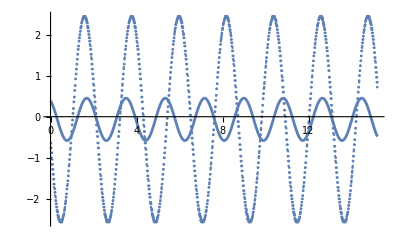

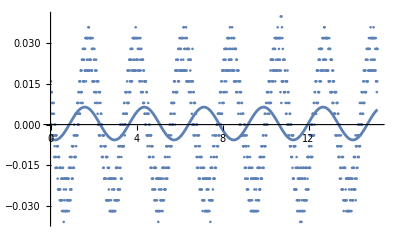

-8.43769×10^-15

-8.52651×10^-14

{{0.515428,0.0639318},{3.44011,0.027345},{2.06495,0.241283},{-0.0645547,0.0448595}}

```mathematica
dat=Import[filenms[[90]]][[5;;-1]];
dat1={#[[1]]/samplerate,#[[2]]}&/@dat[[All,1;;2]];
dat2={#[[1]]/samplerate,#[[2]]}&/@dat[[All,{1,3}]];
fit1 = NonlinearModelFit[dat1, a Sin[b t+ c] + d  , {{a,Max[dat1[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat1,Last][[1,1]]/Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
fit2 = NonlinearModelFit[dat2, a Sin[b t+ c] + d , {{a,Max[dat2[[All,2]]]},{b,0.9 2 π /Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]},{c,2π MaximalBy[dat2,Last][[1,1]]/Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]-π/2},{d,0}},t];
Show[ListPlot[{dat2}],Plot[{fit2[t]},{t,0,dat1[[-1,1]]},PlotRange->All]]
Show[ListPlot[{dat1}],Plot[{fit1[t]},{t,0,dat1[[-1,1]]},PlotRange->All]]
Total[fit1["FitResiduals"]]
Total[fit2["FitResiduals"]]
Transpose[{fit2["BestFitParameters"][[All,2]],fit2["ParameterErrors"]}]
```

```mathematica
{}
```

{{0.515428,0.0639318},{0.0344011,0.00027345},{2.06495,0.241283},{-0.0645547,0.0448595}}

{{0.0382655,0.000214789,0.942532,0.0014807,0.537991,0.0126472,0.000196018,0.000159917,-2.49377,0.000799866,0.942443,0.000064447,2.25649,0.000576039,-0.0630178,0.000551623},{0.040389,0.000220246,0.974534,0.00135678,0.281526,0.011606,0.000334305,0.0001601,-2.49412,0.000807916,0.973882,0.0000672509,2.0177,0.000598434,-0.0624431,0.000562253},{-0.0425379,0.000223912,1.00498,0.0012315,15.7405,0.0105747,0.000417703,0.000159683,2.49318,0.00080909,1.00534,0.0000709495,4.91636,0.000627197,-0.0616413,0.000570364},{0.0447688,0.000221218,1.03679,0.00109189,6.0575,0.00943924,0.000285646,0.000155655,2.49268,0.00081552,1.03672,0.0000759676,4.67712,0.00066643,-0.0627916,0.000583499},{0.0472382,0.000234221,1.06836,0.00105223,-0.481998,0.00917389,0.000405441,0.000163749,2.49471,0.000797477,1.06813,0.0000784993,4.43833,0.000683921,-0.0619586,0.00057861},{-0.0498118,0.000223815,1.09952,0.00093594,2.40484,0.00823107,0.000419757,0.000156444,2.49397,0.000806696,1.09959,0.0000825374,4.19847,0.000715791,-0.0627184,0.000590695},{0.052534,0.000226553,1.13066,0.000901826,17.8576,0.0079916,0.000263389,0.000159135,2.49407,0.000818853,1.13094,0.0000847035,3.9591,0.00073339,-0.0622929,0.000600264},{0.0554192,0.000227555,1.16263,0.000880613,17.5913,0.00784687,0.000364454,0.000161304,2.49356,0.000844047,1.16235,0.0000857762,3.72048,0.000743815,-0.062103,0.000614232},{-0.0584335,0.000234826,1.1938,0.00089577,1.62281,0.00800105,0.000388644,0.000168318,2.49336,0.000883016,1.19382,0.0000862162,3.48158,0.000750794,-0.0622166,0.000634402},{0.0615046,0.000224996,1.22554,0.000851862,10.7788,0.00760194,0.000423826,0.000163081,-2.49256,0.000944614,1.2252,0.0000877302,6.38305,0.00076835,-0.0629384,0.000669204},{0.065052,0.00022347,1.25644,0.000829333,4.23336,0.00736823,0.00029022,0.000163254,-2.49247,0.000989682,1.25659,0.0000875435,6.14171,0.000771335,-0.0637181,0.000692861},{0.0686845,0.000225405,1.28811,0.00080939,3.96218,0.0071355,0.000283796,0.000165101,-2.49297,0.00104036,1.28811,0.0000885915,5.90452,0.000784847,-0.064036,0.000722612},{0.0723782,0.000224203,1.31957,0.000765234,3.68879,0.00667913,0.000343639,0.000163658,-2.49126,0.00108742,1.31942,0.0000908018,5.66583,0.000806974,-0.0630452,0.000752863},{0.0765086,0.000227904,1.35063,0.000724588,3.41163,0.00625788,0.000385353,0.000165077,-2.49124,0.00112489,1.35088,0.0000939032,5.42348,0.00083497,-0.0625762,0.000779811},{-0.0806107,0.000223324,1.38244,0.000657429,12.5516,0.00562417,0.000325359,0.000160296,2.48979,0.00113561,1.38227,0.0000966708,8.32544,0.000857741,-0.0606547,0.000791461},{-0.0850729,0.000226054,1.4137,0.000614958,5.98929,0.0052324,0.000376917,0.000161023,2.48929,0.00113916,1.4137,0.000100365,8.08934,0.00088653,-0.062556,0.000800789},{0.0894566,0.000227096,1.44511,0.000575966,21.4031,0.00490045,0.000383028,0.000160971,2.48786,0.00114461,1.44513,0.000105267,1.56293,0.000925104,-0.0621278,0.000813106},{0.093944,0.000229014,1.47664,0.000547927,8.54278,0.00469083,0.000328251,0.000162086,2.48674,0.00113451,1.47657,0.000108798,1.3245,0.000951104,-0.0617701,0.000814311},{0.0984636,0.000223148,1.50799,0.000510657,8.24416,0.00441981,0.000365211,0.000158201,2.4852,0.00113479,1.50797,0.000112304,1.08687,0.000977832,-0.0630229,0.000820715},{0.10296,0.000227196,1.53964,0.000503129,14.221,0.004413,0.000286183,0.000161679,2.48408,0.00115761,1.53936,0.000116092,0.84865,0.0010089,-0.062426,0.000839323},{0.106872,0.000230021,1.57073,0.000498109,1.34299,0.00442251,0.000330265,0.000164317,2.48014,0.0011605,1.57082,0.000115641,0.606751,0.00100538,-0.0619133,0.0008386},{-0.110781,0.000229925,1.6024,0.000483961,16.7311,0.00433573,0.000295795,0.000164425,2.4815,0.00116572,1.6021,0.00011317,0.36557,0.000986249,-0.0624886,0.000835739},{0.11355,0.000228751,1.63375,0.000466434,0.70298,0.00419551,0.000371394,0.000163041,2.47891,0.0011875,1.63363,0.000111309,0.125658,0.00097399,-0.0604833,0.000842877},{0.11581,0.000230038,1.66506,0.000450299,0.382171,0.00404686,0.000344897,0.000162838,-2.47827,0.0012231,1.66506,0.000110447,3.02997,0.000971121,-0.0616326,0.000860022},{0.1172,0.000238661,1.69658,0.000449118,0.0561392,0.0040177,0.000345164,0.000167639,-2.47692,0.00121675,1.6964,0.000106571,2.79156,0.000941085,-0.0622448,0.000849616},{-0.117377,0.000242798,1.71228,0.000450419,3.03281,0.00401702,0.000314408,0.000169984,2.47651,0.00124405,1.71212,0.000107761,12.0953,0.000953173,-0.0619946,0.000866714},{-0.117391,0.000236032,1.7278,0.000433424,9.15526,0.00385357,0.000280497,0.000164847,2.47683,0.00126927,1.72786,0.000109089,11.9767,0.000966181,-0.0629418,0.000883071},{-0.117119,0.000235705,1.74355,0.000430746,2.70518,0.00381854,0.000361533,0.000164355,-2.47673,0.00126398,1.74359,0.000108227,2.42884,0.000959261,-0.061054,0.000878989},{-0.116571,0.00024456,1.75928,0.000447805,2.54335,0.00395975,0.000349081,0.00017045,-2.47695,0.00126946,1.75928,0.000108704,2.31015,0.000963746,-0.0608714,0.000883185},{-0.116299,0.00023281,1.76564,0.000427367,8.76238,0.00377562,0.000428812,0.000162282,-2.47742,0.0012779,1.76546,0.000109531,2.26482,0.000971011,-0.0605898,0.000889424},{0.115921,0.000230127,1.772,0.000424162,24.4048,0.00374439,0.000375226,0.000160456,2.47667,0.00128033,1.77187,0.000109972,11.6393,0.000974811,-0.0618536,0.000891618},{-0.115726,0.000237709,1.77841,0.000439497,2.34492,0.00387737,0.000323621,0.00016581,2.4768,0.00128494,1.77812,0.000110625,11.5898,0.000980425,-0.0629763,0.00089544},{0.115201,0.000231865,1.78437,0.00043158,17.994,0.00380518,0.000294953,0.000161829,2.4752,0.00128635,1.78454,0.000111151,11.5438,0.000984716,-0.0617123,0.000897156},{-0.114774,0.000238843,1.79072,0.000447491,2.22077,0.00394355,0.000254754,0.000166823,-2.47643,0.00127481,1.79069,0.000110478,2.07164,0.000978407,-0.0614454,0.000889918},{0.114475,0.000227055,1.79704,0.000427971,24.1439,0.00377047,0.000276387,0.000158728,2.47663,0.0012746,1.79699,0.000110899,5.16276,0.000981771,-0.0620091,0.000890709},{0.113953,0.000232203,1.80329,0.000441474,24.0815,0.00388802,0.000272861,0.000162495,2.47658,0.00129229,1.80329,0.000112948,5.11639,0.000999336,-0.0622751,0.000904109},{0.113426,0.000227979,1.80959,0.000437475,17.7344,0.00385184,0.000327842,0.000159725,2.47717,0.00127563,1.80961,0.000112023,5.06693,0.000990628,-0.0619332,0.000893582},{0.112973,0.000231688,1.81589,0.000448676,5.10595,0.00394942,0.000282995,0.000162531,2.47663,0.00126413,1.81587,0.000111631,17.5867,0.000986486,-0.0632664,0.000886709},{0.112339,0.000223902,1.82225,0.000438501,5.04246,0.00385918,0.00034472,0.000157288,-2.47659,0.00128026,1.82211,0.0001137,26.9642,0.00100407,-0.0633014,0.000899293},{0.111646,0.00023374,1.82854,0.000463348,4.97659,0.00407798,0.000297249,0.000164441,2.47804,0.00128429,1.82832,0.000114672,4.92571,0.00101192,-0.0608343,0.000903465},{0.11109,0.000233632,1.83435,0.000468142,4.91863,0.00411982,0.000338592,0.0001646,2.4779,0.00127811,1.83466,0.000114852,4.87763,0.00101271,-0.0620987,0.00090053},{-0.110377,0.000228867,1.84087,0.000464666,26.8453,0.00408881,0.000288806,0.000161512,2.47882,0.00127805,1.84089,0.000115546,4.83017,0.00101801,-0.0629703,0.000901933},{0.109728,0.00023266,1.8473,0.0004784,4.78977,0.00420949,0.000249483,0.000164466,2.47713,0.00129309,1.84737,0.000117788,11.0653,0.00103681,-0.0630119,0.000914096},{0.109122,0.000224057,1.85358,0.000466399,4.72395,0.00410434,0.000330602,0.00015865,2.47869,0.0012756,1.85349,0.000116886,4.73335,0.00102814,-0.0616253,0.000903204},{0.108284,0.000231595,1.85993,0.000489145,17.2287,0.0043038,0.000309497,0.000164268,2.47781,0.00128731,1.8598,0.000118804,4.68541,0.00104411,-0.0609522,0.000913035},{0.10768,0.000229625,1.86616,0.000490952,4.60247,0.00431876,0.000337374,0.000163141,2.47811,0.00127195,1.86615,0.000118172,4.63849,0.00103759,-0.0626776,0.000903673},{0.106868,0.000226815,1.87246,0.000491842,4.53935,0.00432606,0.000189617,0.00016141,2.47907,0.00129492,1.87235,0.000121051,4.59207,0.00106194,-0.063907,0.000921503},{0.106045,0.000229762,1.87875,0.000505279,4.47671,0.00444343,0.000318921,0.000163767,2.47845,0.00128332,1.87871,0.000120786,4.54167,0.00105883,-0.0629383,0.000914748},{-0.105333,0.000222844,1.88507,0.000496389,26.4079,0.00436356,0.000225004,0.000159079,2.47936,0.00127641,1.88497,0.000120843,4.49595,0.00105838,-0.0627371,0.000911241},{0.104479,0.000225388,1.89105,0.000508893,4.35747,0.00447212,0.000391414,0.000161114,2.47877,0.00128108,1.89117,0.000122033,4.44713,0.00106807,-0.0622945,0.000915933},{-0.103754,0.000221742,1.89748,0.00050688,26.2859,0.00445246,0.000333597,0.000158723,2.47952,0.00129657,1.8975,0.000124177,4.39922,0.00108601,-0.062902,0.000928328},{0.102785,0.0002177,1.90377,0.000504746,16.8002,0.00443141,0.000360359,0.000156018,2.4806,0.00127653,1.90381,0.000122853,4.35178,0.00107365,-0.0628971,0.000915185},{0.102006,0.000223046,1.90993,0.000523292,10.4587,0.00459135,0.000259036,0.000160017,2.48089,0.0012717,1.91004,0.000122963,4.30456,0.00107391,-0.0629665,0.000912803},{0.101135,0.000221652,1.91661,0.000526499,10.3913,0.00461665,0.000304237,0.000159167,2.48094,0.00129069,1.91631,0.000125336,4.25433,0.00109407,-0.0626896,0.00092741},{0.100411,0.000225335,1.92274,0.00054081,10.3363,0.00473807,0.000236411,0.000161936,2.48119,0.00128266,1.92268,0.000125027,4.20786,0.00109071,-0.0622365,0.000922498},{0.0994852,0.000226012,1.92907,0.000548809,3.9911,0.00480434,0.000268699,0.000162517,2.48184,0.00128708,1.92892,0.00012583,4.15967,0.00109721,-0.0610572,0.00092638},{0.0986732,0.000222646,1.93517,0.00054611,3.93459,0.00477638,0.000284507,0.000160166,2.4815,0.00128975,1.93517,0.000126442,4.11488,0.00110205,-0.0626994,0.000928851},{0.0978878,0.000222431,1.94154,0.000550588,3.87241,0.00481105,0.00032523,0.000160049,2.48251,0.00129704,1.94143,0.000127359,4.06337,0.00110973,-0.0639267,0.00093449},{0.096965,0.000228254,1.94751,0.000570691,3.81559,0.00498196,0.00018415,0.000164252,2.48286,0.00130969,1.94773,0.000128763,4.01646,0.00112164,-0.0638116,0.000943841},{0.0216579,0.00244111,2.54182,0.0247403,2.43503,0.217297,-0.00102898,0.00171069,2.4816,0.00131402,1.96347,0.000129329,3.89551,0.00112617,-0.0626126,0.000946779},{0.0207159,0.00238755,2.55719,0.0252305,2.27421,0.221976,-0.000864635,0.00167251,2.48335,0.0013092,1.97919,0.000128321,3.77639,0.00111752,-0.0628703,0.000942087},{-0.0905009,0.000219694,1.99476,0.000581013,12.8018,0.00503156,0.000357534,0.00015748,0.538907,0.0641053,2.56988,0.0258081,2.42635,0.228028,-0.0667314,0.0448025},{-0.0883576,0.000221076,2.01045,0.000593246,6.37389,0.00512613,0.000392083,0.000158067,-2.48522,0.00137188,2.01062,0.000132025,6.67815,0.00115155,-0.0632655,0.000981932},{0.0840528,0.000223766,2.04221,0.000617502,28.081,0.00532346,0.000301543,0.000159076,-2.48622,0.00140946,2.0421,0.000131929,6.43928,0.0011542,-0.0620878,0.00100125},{-0.080018,0.00022775,2.07352,0.000646271,5.8099,0.00557814,0.00035203,0.000161064,-2.48714,0.00148316,2.07343,0.00013465,6.19921,0.00118231,-0.0627121,0.00104557},{0.0762513,0.000230751,2.10499,0.000675747,33.8096,0.00586232,0.000331447,0.000162551,-2.48947,0.00153697,2.10482,0.000135755,5.96005,0.00119637,-0.0621911,0.00107682},{0.0725549,0.000229516,2.13636,0.000699677,20.9745,0.00611846,0.000319773,0.000161346,-0.489768,0.0613265,2.7392,0.0295861,4.27545,0.258811,-0.0598467,0.0438033},{0.0691505,0.000229359,2.16728,0.000732472,8.14704,0.00646269,0.000241527,0.000161207,2.49141,0.00162335,2.16765,0.000140002,8.62442,0.00123884,-0.062286,0.00113231},{-0.0658148,0.00023042,2.1991,0.000777903,4.73463,0.00692032,0.000228294,0.000162215,2.49222,0.00164808,2.19907,0.000143132,8.38167,0.00126606,-0.062705,0.00115207},{0.0626217,0.000224764,2.23046,0.0008057,13.9013,0.00720673,0.000247197,0.000158635,2.49329,0.00165282,2.23058,0.000146151,8.14264,0.00129018,-0.0601745,0.00116082},{0.0597506,0.000226194,2.2617,0.000860019,1.07433,0.00770534,0.000369806,0.000160118,2.4941,0.00164372,2.26191,0.00014905,1.61857,0.00131186,-0.0620779,0.00116178},{0.0569984,0.000224925,2.29366,0.000906097,7.09916,0.00809614,0.000293355,0.000159648,2.49441,0.0016495,2.2933,0.000153676,1.37902,0.00134792,-0.0628696,0.0011738},{0.0544558,0.000227349,2.32476,0.000966059,19.421,0.00857621,0.000312516,0.000161693,2.49523,0.00165327,2.3248,0.00015753,1.14415,0.00137721,-0.0640982,0.0011832},{0.0520511,0.000228651,2.35629,0.00101993,0.316497,0.0089746,0.00025739,0.000162778,2.49689,0.00166524,2.35609,0.000160623,0.903525,0.00140146,-0.0630487,0.0011954},{-0.0497002,0.000224138,2.38838,0.00104683,22.0512,0.00912277,0.000353412,0.000159574,2.49761,0.00168083,2.38764,0.000162104,0.660716,0.00141347,-0.0626375,0.00120607},{0.0475542,0.000221137,2.41902,0.00107653,-0.177099,0.00930905,0.000471884,0.000157337,0.533429,0.0641363,2.99668,0.0262508,-0.827647,0.231783,-0.0616779,0.0448937},{-0.0455023,0.000224385,2.45022,0.00113525,9.00235,0.0097719,0.000260641,0.000159419,-2.49832,0.00171761,2.45046,0.000160117,-2.9572,0.00140054,-0.0609898,0.0012207},{0.0435076,0.000221789,2.48203,0.0011653,37.0275,0.0100285,0.000314007,0.000157279,-2.49919,0.00174297,2.48186,0.000158401,3.08437,0.00138958,-0.0633674,0.00123078},{-0.0417696,0.000218553,2.51287,0.00118775,2.23266,0.0102643,0.000261254,0.000154689,-2.50104,0.00171225,2.51329,0.000151935,2.84318,0.00133701,-0.0625117,0.00120242},{-0.0399938,0.00021989,2.5446,0.0012407,8.27406,0.0108043,0.000329379,0.000155379,-2.49995,0.00178574,2.54469,0.000155943,2.60676,0.00137597,-0.062393,0.00124949},{-0.0383729,0.000222897,2.5755,0.00130707,1.75393,0.0114837,0.000376137,0.00015737,-2.50142,0.00179933,2.57613,0.000156003,2.36673,0.00137853,-0.0606152,0.00125752},{-0.0034597,0.000975984,1.16214,0.0640474,9.12888,0.5484,-0.000750548,0.000699692,2.50099,0.00179975,2.60754,0.000156738,5.26657,0.00138514,-0.0615888,0.00125953},{0.0354792,0.000215792,2.63833,0.00137423,4.41767,0.0122514,0.000338959,0.000152475,2.50082,0.00180167,2.63893,0.000159137,5.0269,0.00140451,-0.0632142,0.00126542},{0.0340385,0.00022007,2.67015,0.00146904,16.7481,0.0131301,0.000241761,0.000155707,2.50245,0.00182007,2.67029,0.000164032,4.79049,0.00144414,-0.063733,0.00128498},{0.0327349,0.000221908,2.70099,0.00155028,35.3688,0.0138359,0.000300775,0.000157262,2.50217,0.00180628,2.7018,0.000166626,4.55071,0.00146268,-0.0620963,0.00128265},{0.0313626,0.000215649,2.73266,0.00158216,16.2837,0.0140486,0.000245761,0.000153071,2.50275,0.00181334,2.73311,0.000170644,4.31026,0.00149387,-0.0619225,0.00129417},{-0.0303159,0.000217559,2.76491,0.00165836,19.1831,0.0146122,0.000310589,0.000154606,2.50373,0.00181983,2.7646,0.000173371,4.06772,0.00151464,-0.0617528,0.0013028},{0.0289993,0.000222766,2.79581,0.00177881,9.53237,0.0155454,0.000266451,0.000158398,2.50377,0.00185421,2.79608,0.000177023,3.83089,0.00154507,-0.0598207,0.00132772},{0.000136506,0.000752202,282.99,1.25789,531.199,11.0313,-5.29855×10^-6,0.000532105,2.50424,0.00188457,2.82744,0.000178337,3.59398,0.00155725,-0.0628162,0.00134593},{0.00607162,0.000707093,2.2679,0.0265092,29.3779,0.237094,0.000394614,0.000500765,0.515428,0.0639318,3.44011,0.027345,2.06495,0.241283,-0.0645547,0.0448595},{-0.00280507,0.000697306,1.44907,0.0570971,1.22489,0.511203,0.000459368,0.000496094,-0.499434,0.0634732,3.47599,0.0284095,4.93784,0.250333,-0.0614941,0.0446939},{-0.00252265,0.000671598,1.47036,0.0624292,7.30937,0.557168,0.00059891,0.000480338,-2.50464,0.00208368,2.92165,0.000185895,6.01211,0.00163416,-0.0613441,0.00146579},{-0.00242408,0.000647932,1.49503,0.0636287,19.6306,0.564786,0.000596209,0.000465241,2.505,0.00211344,2.95309,0.000185632,8.91712,0.00163598,-0.0611107,0.0014815},{0.0232564,0.000228502,2.98427,0.00219578,8.17703,0.0192908,0.000199567,0.000160955,2.50569,0.00214497,2.98447,0.00018697,8.68193,0.00165041,-0.0647677,0.00150139}}

```mathematica
Differences[Select[dat2,#[[2]]>0.90 Max[dat2[[All,2]]]&][[All,1]]]
```

```mathematica
Select[dat2,#[[2]]>0.90 Max[dat2[[All,2]]]&][[All,1]]
Differences[Select[dat2,#[[2]]>0.90 Max[dat2[[All,2]]]&][[All,1]]]
```

{168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,198,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,620,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,830,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023,1024,1025,1026,1027,1028,1029,1030,1031,1032,1033,1034,1035,1036,1037,1038,1040,1220,1221,1222,1223,1224,1225,1226,1227,1228,1229,1230,1231,1232,1233,1234,1235,1236,1237,1238,1239,1240,1241,1242,1243,1244,1245,1246,1247,1248,1249,1250,1252,1432,1433,1434,1435,1436,1437,1438,1439,1440,1441,1442,1443,1444,1445,1446,1447,1448,1449,1450,1451,1452,1453,1454,1455,1456,1457,1458,1459,1460,1462}

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,180,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2}

```mathematica
D[Sin[ω t + ϕ],{t,2}]
```

-ω^2 Sin[ϕ+t ω]

```mathematica
Solve[{Cos[ϕ+t ω]==0,Sin[ϕ+t ω]<0},ϕ]
```

{{ϕ→ConditionalExpression[1/2 (-π-2 t ω+4 π C[1]), C[1]∈ℤ]},{ϕ→ConditionalExpression[1/2 (-π-2 t ω+4 π (C[1]-C[2])), (C[1]|C[2])∈ℤ&&C[1]≥0&&C[2]≥0]}}

192

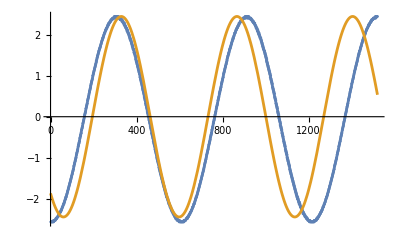

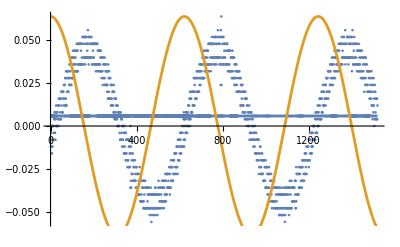

```mathematica
rl1=Evaluate[{a->Max[dat2[[All,2]]],b->0.9 2 π /Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]],c->-2π MaximalBy[dat2,Last][[1,1]]/Max[Differences[Select[dat2,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]+π/2,d->0}];
rl2=Evaluate[{a->Max[dat1[[All,2]]],b->0.9 2 π /Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&][[All,1]]]],c->-2π MaximalBy[dat1,Last][[1,1]]/Max[Differences[Select[dat1,#[[2]]>0.8 Max[dat2[[All,2]]]&][[All,1]]]]+π/2,d->0}];
Show[ListPlot[{dat2}],Plot[{fit2[t],(a Sin[b t+ c] + d)/.rl1},{t,0,dat1[[-1,1]]},PlotRange->All]]
Show[ListPlot[{dat1}],Plot[{fit1[t],(a Sin[b t+ c] + d)/.rl2},{t,0,dat1[[-1,1]]},PlotRange->All]]
```

```mathematica
Max[Differences[Select[dat1,#[[2]]>0.90 Max[dat1[[All,2]]]&][[All,1]]]]
```

-∞

```mathematica
Differences[Select[dat1,#[[2]]>0.90 Max[dat1[[All,2]]]&][[All,1]]]
```

{}

```mathematica
Select[dat1,#[[2]]>0.8 Max[dat1[[All,2]]]&]
```

{{148,0.052},{152,0.052},{154,0.052},{156,0.052},{158,0.052},{162,0.052},{164,0.052},{166,0.052},{174,0.056},{176,0.052},{178,0.052},{182,0.052},{188,0.052},{190,0.052},{750,0.052},{760,0.052},{764,0.052},{766,0.052},{768,0.052},{776,0.052},{778,0.056},{780,0.052},{786,0.052},{790,0.052},{792,0.056},{794,0.064},{796,0.052},{798,0.052},{802,0.052},{804,0.052},{1354,0.052},{1362,0.052},{1364,0.052},{1370,0.056},{1378,0.052},{1380,0.052},{1382,0.052},{1384,0.052},{1388,0.052},{1394,0.052},{1398,0.052},{1402,0.052},{1404,0.056},{1412,0.052}}